# Trigonometric circle

```mathematica
θ=π/6(*Radian*);
```

### Formuls

```mathematica
p={Cos[θ],Sin[θ]};
```

```mathematica
circle=Graphics[Circle[]];
```

```mathematica
SinAxis=Graphics[{Arrow[{{0,-2},{0,2}}],Text["Sin x",{0,2.1}]}];
```

```mathematica
CosAxis=Graphics[{Arrow[{{-2,0},{2,0}}],Text["Cos x",{2.2,0}]}];
```

```mathematica
TanAxis=Graphics[{Arrow[{{1,-2},{1,2}}],Text["Tan x",{1,2.1}]}];
```

```mathematica
CotAxis=Graphics[{Arrow[{{-2,1},{2,1}}],Text["Cot x",{2.2,1}]}];
```

```mathematica
point=ListPlot[{p},PlotRange->{{-1,1},{-1,1}},MeshStyle->Red,PlotMarkers->{Automatic,Medium}];
```

```mathematica
l1=Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]}];
```

```mathematica
l2=Graphics[{Blue,Thick,Line[{{0,0},3p}]}];
```

```mathematica
SinDotted=Graphics[{Dotted,Blue,Line[{{Cos[θ],Sin[θ]},{0,Sin[θ]}}]}];
```

```mathematica
CosDotted=Graphics[{Dotted,Blue,Line[{{Cos[θ],Sin[θ]},{Cos[θ],0}}]}];
```

```mathematica
TanAndCotDotted=Graphics[{Dotted,Blue,Line[{{0,0},3{-Cos[θ],-Sin[θ]}}]}];
```

```mathematica
SinValue=Graphics[{Pink,Arrowheads[Medium],Arrow[{{0,0},{0,Sin[θ]}}]}];
```

```mathematica
CosValue=Graphics[{Pink,Arrowheads[Medium],Arrow[{{0,0},{Cos[θ],0}}]}];
```

```mathematica
TanValue=Graphics[{Pink,Arrowheads[Medium],Arrow[{{1,0},{1,Tan[θ]}}]}];
```

```mathematica
CotValue=Graphics[{Pink,Arrowheads[Medium],Arrow[{{0,1},{Cot[θ],1}}]}];
```

```mathematica
α=PolarPlot[0.3,{α,0,θ}];
```

```mathematica
Arc=Graphics[{Thick,Circle[{0,0},1,{0,θ}]}];
```

```mathematica
TrigoFunctions=MatrixForm[({{"Sin[θ]=", Sin[θ]}, {"Cos[θ]=", Cos[θ]}, {"Tan[θ]=", Tan[θ]}, {"Cot[θ]=", Cot[θ]}})];
```

```mathematica
show=Show[circle,SinAxis,CosAxis,TanAxis,CotAxis,point,l1,l2,SinDotted,CosDotted,TanAndCotDotted,SinValue,CosValue,TanValue,CotValue,α,Arc,ImageSize->Large];
```

### Show

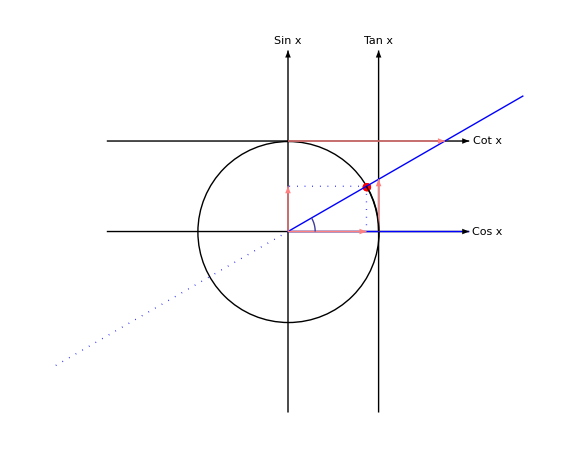

```mathematica
show
```

```mathematica
TrigoFunctions
```

(Sin[θ]= | 1/2
Cos[θ]= | (√3)/2
Tan[θ]= | 1/(√3)
Cot[θ]= | √3)

```mathematica
N[TrigoFunctions]
```

(Sin[θ]= | 0.5
Cos[θ]= | 0.866025
Tan[θ]= | 0.57735
Cot[θ]= | 1.73205)